```mathematica
(* derive expression for dBz/dx *)
(*integrand=(-Cos[ϕ](1+u^2+v^2-2u Cos[ϕ])+(1-u Cos[ϕ])(-3/2)(2u-2Cos[ϕ]))/((1+u^2+v^2-2u Cos[ϕ])^(5/2))//Simplify; *)
indefIntdBzdx =  (μ J)/(4π a^2)Integrate[(-3 u+(2+2 u^2-v^2) Cos[ϕ]-u Cos[ϕ]^2)/((1+u^2+v^2-2 u Cos[ϕ])^(5/2)),ϕ];
dBzdx = indefIntdBzdx/.ϕ->2π-indefIntdBzdx/.ϕ->0
```

(J μ (8 u^2 (1+u^4-2 v^2-3 v^4-2 u^2 (1+v^2)) EllipticK[-(4 u)/(1-2 u+u^2+v^2)]+(u^6+(1+v^2)^2+u^4 (-1+2 v^2)+u^2 (-1-12 v^2+v^4)) (2 (1-2 u+u^2+v^2) EllipticE[-(4 u)/(1-2 u+u^2+v^2)]-2 (1+u^2+v^2) EllipticK[-(4 u)/(1-2 u+u^2+v^2)])))/(4 a^2 π u (1-2 u+u^2+v^2)^(5/2) (1+2 u+u^2+v^2)^2)

```mathematica
(* derive expression for dBx/dx*)
indefIntdBxdx = (μ J)/(4π a^2)Integrate[(3 Cos[ϕ] (-u+Cos[ϕ]))/((1+u^2+v^2-2 u Cos[ϕ])^(5/2)),ϕ];
dBxdx = indefIntdBxdx/.ϕ->2π-indefIntdBxdx/.ϕ->0
```

(J μ (4 u^2 (-7 u^4-6 u^2 (-1+v^2)+(1+v^2)^2) EllipticK[-(4 u)/(1-2 u+u^2+v^2)]-(2 u^6+5 u^4 (1+v^2)+(1+v^2)^3+4 u^2 (-2-v^2+v^4)) (2 (1-2 u+u^2+v^2) EllipticE[-(4 u)/(1-2 u+u^2+v^2)]-2 (1+u^2+v^2) EllipticK[-(4 u)/(1-2 u+u^2+v^2)])))/(4 a^2 π u^2 (1-2 u+u^2+v^2)^(5/2) (1+2 u+u^2+v^2)^2)

```mathematica
(* now derive formulas for dBx/dz and dBz/dz, which were first encountered in case of magnet //z *)

indefIntdBxdz =  (μ J)/(4π a^2)Integrate[(1+u^2-2 v^2-2u Cos[ϕ])/((1+u^2+v^2-2 u Cos[ϕ])^(5/2))Cos[ϕ],ϕ];
dBxdz =indefIntdBxdz/.ϕ->2π-indefIntdBxdz/.ϕ->0

indefIntdBzdz =  (μ J)/(4π a^2)Integrate[(-3v(1-u Cos[ϕ]))/((1+u^2+v^2-2 u Cos[ϕ])^(5/2)),ϕ];
dBzdz = indefIntdBzdz/.ϕ->2π-indefIntdBzdz/.ϕ->0
```

(J μ (8 u^2 (1+u^4-2 v^2-3 v^4-2 u^2 (1+v^2)) EllipticK[-(4 u)/(1-2 u+u^2+v^2)]+(u^6+(1+v^2)^2+u^4 (-1+2 v^2)+u^2 (-1-12 v^2+v^4)) (2 (1-2 u+u^2+v^2) EllipticE[-(4 u)/(1-2 u+u^2+v^2)]-2 (1+u^2+v^2) EllipticK[-(4 u)/(1-2 u+u^2+v^2)])))/(4 a^2 π u (1-2 u+u^2+v^2)^(5/2) (1+2 u+u^2+v^2)^2)

(J v μ (2 (-7+u^4-6 v^2+v^4+2 u^2 (3+v^2)) EllipticE[-(4 u)/(1-2 u+u^2+v^2)]-2 (-1+2 u^3+u^4+2 u^2 v^2+v^4+2 u (-1+v^2)) EllipticK[-(4 u)/(1-2 u+u^2+v^2)]))/(4 a^2 π (1-2 u+u^2+v^2)^(3/2) (1+2 u+u^2+v^2)^2)

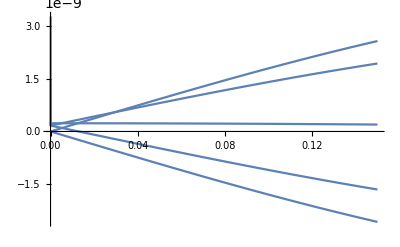

```mathematica
(* now evaluate forces *)
Module[{dBxdx0,dBxdz0,dBzdx0,dBzdz0,J0,m0,μ0,a0},
Alphas = {0,0.8,π/2,π-0.8,π};
choices = {1,2,4π 10^-7,0.05};
{J0,m0,μ0,a0}=choices;
x0 = 0.2 a0;
z0 = 1.0 a0; 
{dBxdx0,dBxdz0,dBzdx0,dBzdz0} = {dBxdx,dBxdz,dBzdx,dBzdz}/.Thread[{J,m,μ,a}->choices];


Fx[x_,z_,α_]:=( m0 Cos[α] dBxdz0 + m0 Sin[α] dBxdx0)/.{u->x/a0,v->z/a0};

Fz[x_,z_,α_]:=(m0 Cos[α] dBzdz0 + m0 Sin[α] dBzdx0)/.{u->x/a0,v->z/a0};

Show[Plot[Fx[x,1,#],{x,0,3a0}]&/@Alphas,PlotRange->All]

]

(*
Plot[Fx[x,1,#],{x,0,3a}]&/@Alphas
mySin[X_,A_,B_]:=Sin[A X + B]
Plot[mySin[X,1, 0],{X,0,2}] 
*)
```

```mathematica
(* derive expression for emf for general off-axis case without prefactor μ/(4π), ring is in x-y plane and magnet at {x,0,z}, ϵ = Integrate[Dot[Cross[v,B],dl],{ϕ,0,2π}] - but assume that v = vz , i.e. neglect radial velocity of magnet *)

M = m{Sin[α],0,Cos[α]}; (* dipole moment vector *)
dldϕ = a{-Sin[ϕ],Cos[ϕ],0};  (* dl/dϕ gives the line element of ring *)
R = {a Cos[ϕ]-x,a Sin[ϕ],-z};   (* relative radius vector of a line element at angle ϕ w.r.t. magnet at {x,0,z} *)
magR2 = Simplify[R⟦1⟧^2+R⟦2⟧^2+R⟦3⟧^2];
B=(3R Dot[M,R]-magR2 M)/magR2^(5/2)//Simplify
{Bx,By,Bz}=B;
 ϵ = Integrate[ vz(By Cos[ϕ]+Bx C+os[ϕ]),{ϕ,0,2π}]
```